4 vertices and 3 edges (less than 3 edges are trivially 0 questions asked since it cant be connected) all function

1+p+p^2

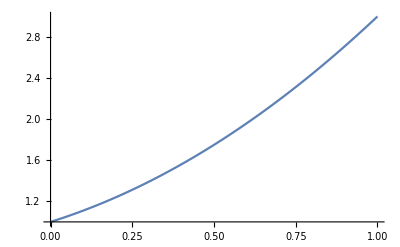

```mathematica
Dconnectnaive3[p_] = 1+p +p^2
Plot[Dconnectnaive3[p],{p,0,1}]
```

4 vertices and 4 edges

3-(1-p)^2+3 (1-p) p^2

1+p (2+2 (1-p) p)

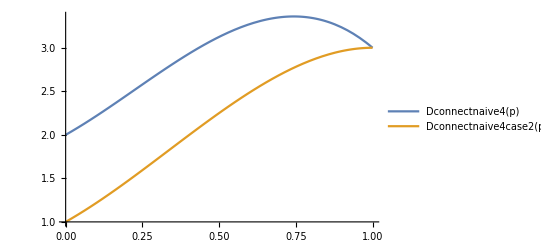

{3.35958,{p→0.74338}}

```mathematica
Dconnectnaive4[p_] = 1+1+(1-(1-p)^2)+3p^2(1-p)
Dconnectnaive4case2[p_] = 1+p(1+1+2p(1-p))
Plot[{Dconnectnaive4[p],Dconnectnaive4case2[p]},{p,0,1},PlotLegends->"Expressions"]
FindMaximum[Dconnectnaive4[p],{p,0.5}]
```

Influence of x1 (deg 3 deg 2) and x5 (deg 3 deg 3) in graph with 4 nodes and 5 edges

5 (1-p)^3 p^2+6 (1-p)^2 p^3+(1-p) p^4

5 p^2-9 p^3+4 p^4

4 (1-p)^3 p^2+4 (1-p)^2 p^3

4 p^2-8 p^3+4 p^4

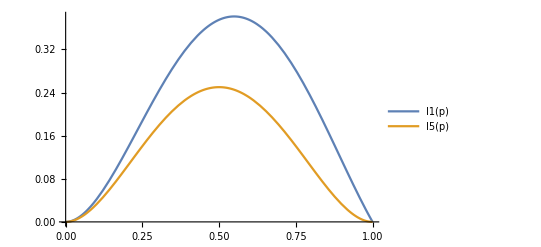

```mathematica
I1[p_]=5p^2(1-p)^3+6p^3(1-p)^2+p^4(1-p)
Expand[I1[p]]
I5[p_] = 4p^2(1-p)^3 + 4p^3(1-p)^2
Expand[I5[p]]
Plot[{I1[p],I5[p]},{p,0,1}, PlotLegends->"Expressions"]
```

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/graphinfluence.png",%228,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/graphinfluence.png

```mathematica
1+p(1+(1-p))+(1-p)(1+p(1+(1-p)))
```

1+(2-p) p+(1-p) (1+(2-p) p)

```mathematica
Expand[1+(2-p) p+(1-p) (1+(2-p) p)]
```

2+3 p-4 p^2+p^3

1+p (2+2 (1-p) (2-p) p)+(1-p) (1+p (2+2 (1-p) p))

2+3 p+4 p^2-10 p^3+4 p^4

2+4 p+2 p^2-9 p^3+4 p^4

2+4 p+3 p^2-10 p^3+4 p^4

1+(1-p) (3-(1-p)^2+3 (1-p) p^2)+p (1+(2-p) p+(1-p) (1+(2-p) p))

3+2 p+3 p^2-9 p^3+4 p^4

4 (1-p) p (4 I1[p]+I5[p])^2

64 p I1[p]^2-64 p^2 I1[p]^2+32 p I1[p] I5[p]-32 p^2 I1[p] I5[p]+4 p I5[p]^2-4 p^2 I5[p]^2

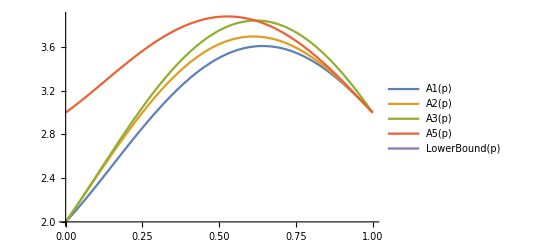

{{p→1.},{p→1.}}

{-3.,-3.}

{-3.,-3.}

{3.60808,{p→0.64245}}

```mathematica
A1[p_]=1+(1-p)(Dconnectnaive4case2[p])+p(2+2p(1-p)(1+(1-p)))
Expand[A1[p]]
A2[p_] = 2+4p+2p^2-9p^3+4p^4
A3[p_] = 2+4p+3p^2-10p^3+4p^4
A5[p_]=1+(1-p)(Dconnectnaive4[p])+p(1+p(1+(1-p))+(1-p)(1+p(1+(1-p))))
Expand[A5[p]]
LowerBound[p_]=4p(1-p)(4I1[p]+I5[p])^2
Expand[LowerBound[p]]
Plot[{A1[p],A2[p],A3[p],A5[p],LowerBound[p]},{p,0,1},PlotLegends->"Expressions"]
intersect1 = NSolve[A1[p]==A5[p]&&p<=1&&p>0]
A1'[p/.intersect1]
A5'[p/.intersect1]
FindMaximum[A1[p],{p,0.5}]
```

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.eps",%113,"EPS"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.eps

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.png",%30,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.png",%52,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/graph5algs.png

1+(1+(1+(1-p) (2-p)) (1-p)) p+(1-p) (1+(2-p) p+(1-p) (1+(2-p) p))

1+(1-p) (1+p (2+2 (1-p) (2-p) p)+(1-p) (1+p (2+2 (1-p) p)))+p (1+(1+(1+(1-p) (2-p)) (1-p)) p+(1-p) (1+(2-p) p+(1-p) (1+(2-p) p)))

1+p (1+(1+(1+(1-p) (2-p)) (1-p)) p+(1-p) (1+(2-p) p+(1-p) (1+(2-p) p)))+(1-p) (1+(1-p) (3-(1-p)^2+3 (1-p) p^2)+p (1+(2-p) p+(1-p) (1+(2-p) p)))

1+p (1+(1+(1+(1-p) (2-p)) (1-p)) p+(1-p) (1+(2-p) p+(1-p) (1+(2-p) p)))+(1-p) Min[1+p (2+2 (1-p) (2-p) p)+(1-p) (1+p (2+2 (1-p) p)),1+(1-p) (3-(1-p)^2+3 (1-p) p^2)+p (1+(2-p) p+(1-p) (1+(2-p) p))]

3+4 p+6 p^2-27 p^3+23 p^4-6 p^5

4+2 p+6 p^2-25 p^3+22 p^4-6 p^5

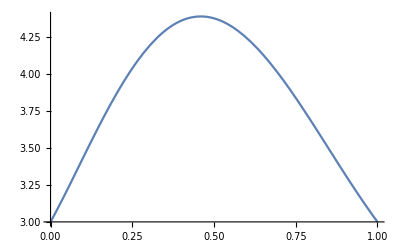

{4.38777,{p→0.459499}}

```mathematica
A[p_]=1+(1-p)(1+(1-p)(1+p(1+(1-p)))+p(1+(1-p)))+p(1+(1-p)(1+(1-p)(1+(1-p))))
A61[p_]=1+(1-p)A1[p]+p A[p]
A62[p_]=1+(1-p)A5[p]+p A[p]
A6[p_]=1+(1-p)Min[A1[p],A5[p]]+p A[p]
Expand[A61[p]]
Expand[A62[p]]
Plot[A6[p],{p,0,1}]
FindMaximum[A6[p],{p,0.5}]
```

```mathematica
Expand[1+(1+(1+(1-p) (2-p)) (1-p)) p+(1-p) (1+(2-p) p+(1-p) (1+(2-p) p))]
```

3+5 p-13 p^2+9 p^3-2 p^4

```mathematica
FindMaximum[%30,{{p,0.5}}]
```

{4.50729,{p→0.470976}}